0.000209891

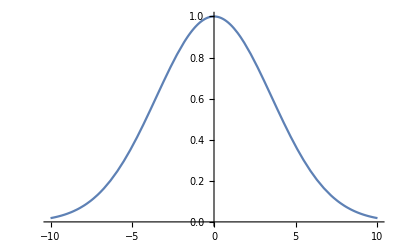

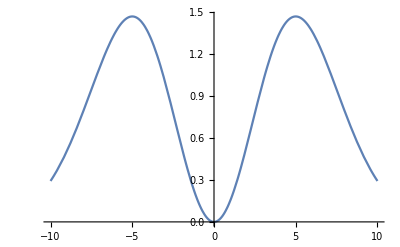

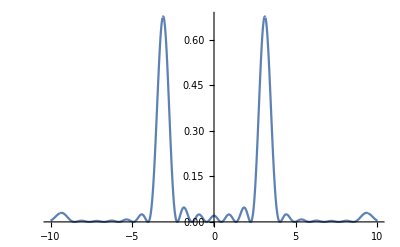

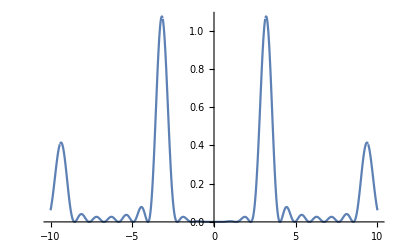

```mathematica
(* d = 1, ℏ = 1, m = 1; things might not be properly normalized *)
dphys = 790*^-9/2; ℏ=1.055*^-34; mRb=1.41923*^-25;
tunit=mRb*dphys^2/ℏ
σWannier=0.2; (* Width of Wannier states in real space (large -> small in momentum space); approximated as a Gaussian *)
Ψ1[p_,σ_]:=Exp[-p^2*σ^2/2]; (* Gaussian approximation of Wannier states, in momentum space *)
Ψ2[p_,σ_]:=I*Exp[-p^2*σ^2/2]*HermiteH[1,p*σ]; (* Hermite-Gaussian approximation of the first excited state, in momentum space (check) *)
Intf[p_,ξ_]:=Cos[(2*ξ+1)*p/2]/(Cos[p/2]*(2*ξ+1)); (* Interference term, normalized at p = 0; (2ξ + 1): sites occupied, assuming uniform filling *)
Ψ[p_,Ψ0_,σ_,ξ_]:=Ψ0[p,σ]*Intf[p,ξ]; (* Full momentum space wave function *)
Ψx[x_,σ_,ξ_,t_]:=FourierTransform[Ψ[p,σ,ξ]*Exp[-I*p^2*t/2],p,x]; (* Real space wave function after ToF with time t, with no approximation; very time consuming to plot *)
Plot[Abs[Ψ1[p,σWannier]]^2,{p,-10,10}]
Plot[Abs[Ψ2[p,σWannier]]^2,{p,-10,10}]
Plot[Abs[Ψ[p,Ψ1,σWannier,3]]^2,{p,-10,10},PlotRange->Full]
Plot[Abs[Ψ[p,Ψ2,σWannier,3]]^2,{p,-10,10},PlotRange->Full]
(*Plot[Abs[Ψx[x,σWannier,20, 29.5*^-3/tunit]]^2,{x,-1300,1300},PlotRange->Full]*)
```